```mathematica
(*Dawid Bitner*)
(*zad1*)
PPL[f_,min_,max_,n_,r_,it_]:=Module[{xbest,tabval,ybest,y,i,tablica={}},
(* Funkcje w zad1, 2 i 4 zostały zbudowane na podstawie pseudokodu z prezentacji z wykładu *)
xbest={RandomReal[{min,max}],RandomReal[{min,max}]}; (*l osowe rozwiązanie podstawe z przedziału podanego przez użytkownika *)
ybest=f[xbest[[1]],xbest[[2]]]; (* ybest na podstawie funkcji i xbest *)
tablica=Join[tablica,{ybest}]; (* dołączenie wyniku do tablicy *)
Do[
(* początek pętli i stworzenie tabeli "sąsiedztwa" *)
tabval=Table[{RandomReal[{xbest[[1]]-r,xbest[[1]]+r}],RandomReal[{xbest[[2]]-r,xbest[[2]]+r}]},{i,1,n}];
(* określamy jakość sąsiedztwa *)
y=Table[f[tabval[[i,1]],tabval[[i,2]]],{i,1,n}];
If[Min[y]<ybest,ybest=Min[y]; (* rozpocyznamy poszukiwanie najlepszej wartości w sąsiedztwie i przypisujemy ją do ybest, wynik dołączamy do tablicy *)
i=Flatten[Position[y,ybest,1,1]][[1]];
xbest=tabval[[i]]];
tablica=Join[tablica,{ybest}];,{i,1,it}];
(* wypisanie wyników *)
Print["Wartości x i y w minimum: ",xbest];
Print["Wartość funkcji w minimum: ",ybest];
ListPlot[tablica]
]
```

```mathematica
(*zad2*)
PPLMulti[f_,min_,max_,n_,r_,multi_,it_]:=Module[{xbest,tabval,ybest,ytab,tab={},xstart,i,j},
(* wybiermay początkowy xbest z podanego przedziału na wejściu *)
xbest=Table[{RandomReal[{min,max}],RandomReal[{min,max}]},{i,1,multi}];
xstart=xbest; (* przypisywanie początkowe, najlepsze x to te startowe *)
ybest=Table[f[xbest[[i,1]],xbest[[i,2]]],{i,1,multi}];
tab=Table[{ybest[[i]]},{i,1,multi}];
For[j=1,j≤multi,j++,
Do[
(* początek pętli i stworzenie tabeli "sąsiedztwa" *)
tabval=Table[{RandomReal[{xbest[[j,1]]-r,xbest[[j,1]]+r}],RandomReal[{xbest[[j,2]]-r,xbest[[j,2]]+r}]},{i,1,n}];
(* określa się jakość sasiedztwa *)
ytab=Table[f[tabval[[i,1]],tabval[[i,2]]],{i,1,n}];
(* poszukujemy najlepszej wartości wśród sąsiedztwa i przypisujemy ją do ybest *)
If[Min[ytab]<ybest[[j]],ybest[[j]]=Min[ytab];
i=Flatten[Position[ytab,ybest[[j]],1,1]][[1]];
xbest[[j]]=tabval[[i]]];
tab[[j]]=Join[tab[[j]],{ybest[[j]]}];,{i,1,it}]];
i=Flatten[Position[ybest,Min[ybest],1,1]][[1]];
Print["Wartości x i y w minimum: ",xbest[[i]]];
Print["Wartość funkcji w minimum: ",Min[ybest]];
ListPlot[tab[[i]]]
]
```

Wartości x i y w minimum: {0.00497647,0.0081459}

Wartość funkcji w minimum: -9.98193

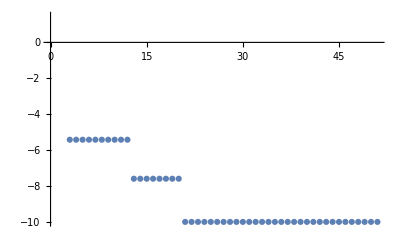

Wartości x i y w minimum: {-0.0229276,-0.00901068}

Wartość funkcji w minimum: -9.87979

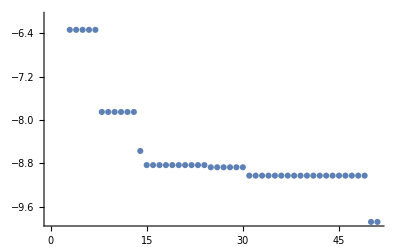

Wartości x i y w minimum: {-0.0450696,0.0352268}

Wartość funkcji w minimum: 0.247045

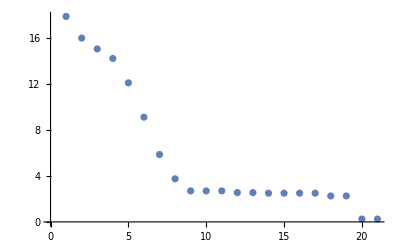

Wartości x i y w minimum: {0.0377272,0.0493366}

Wartość funkcji w minimum: 0.27577

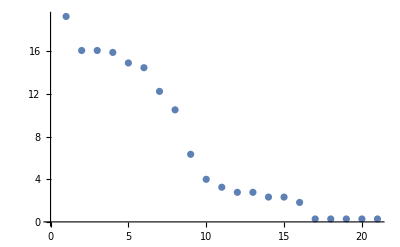

```mathematica
(*zad3*)
(* funkcje testowe *)
RastringerFunction3D[x_,y_]=10+((x^2-10*Cos[2*Pi*x])+(y^2-10*Cos[2*Pi*y]));
AckleyFunction3D[x_,y_]=-20 Exp[-0.2*Sqrt[0.5*(x^2+y^2)]]-Exp[0.5*(Cos[2*Pi*x]+Cos[2*Pi*y])]+E+20;
(* wywołanie PPL *)
PPL[RastringerFunction3D,-5,5,10,2,50]
PPLMulti[RastringerFunction3D,-5,5,10,2,3,50]
PPL[AckleyFunction3D,-10,10,20,2,20]
PPLMulti[AckleyFunction3D,-10,10,20,2,3,20]
```

```mathematica
(*zad4*)
PPLZS[f_,min_,max_,n_,r_,it_,maxchange_]:=Module[{xbest,ybest,tabval,y,ybests={},i,l=1},
xbest={RandomReal[{min,max}],RandomReal[{min,max}]}; (*Wybór rozwiązania początkowego xbest z podanego przedziału min,max*)
ybest=f[xbest[[1]],xbest[[2]]];
ybests=Join[ybests,{ybest}]; (*Dodanie ybest do tablicy wyników ybests*)
Do[
(* pętla do przeszukiwania nastepnych generowanych sąsiedztw *)
Do[
(* początek pętli i stworzenie tabeli "sąsiedztwa" *)
tabval=Table[{RandomReal[{xbest[[1]]-r,xbest[[1]]+r}],RandomReal[{xbest[[2]]-r,xbest[[2]]+r}]},{i,1,it}];
y=Table[f[tabval[[i,1]],tabval[[i,2]]],{i,1,it}]; (* określamy jakość sąsiedztwa *)
If[Min[y]<ybest,ybest=Min[y]; (* szukanie najlepszej wartości wśród sąsiedztwa i przypisanie jej do ybest *)
xbest=tabval[[Flatten[Position[y,ybest,1,1]][[1]]]];
ybests=Join[ybests,{ybest}];
l=1;,l++;];,{l,1,maxchange}];,{i,1,n}];
(* od i do zadanego n, Prawda/Fałsz, jeżeli w wylosowanym sasiedztwie znajduje się najlepsza wartość to 
iteracja wraca do wartości startowej czyli 1, w przeciwnym wypadku losujemy nowe sasiedztwo dla xbest a licznik zwiekszamy o 1 - aż do osięgnięcia maxchange *) Print["Argumenty x i y w minimum: ",xbest];
Print["Wartości funkcji w minimum: ",ybest];
Print[ListPlot[ybests]]
;]
```

Argumenty x i y w minimum: {-0.99495,-0.0000216692}

Wartości funkcji w minimum: -9.00504

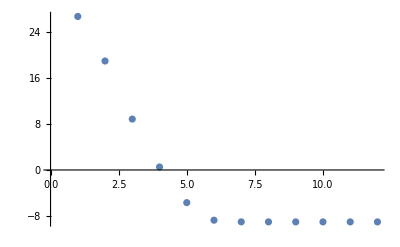

Argumenty x i y w minimum: {0.992781,3.97083}

Wartości funkcji w minimum: 8.81315

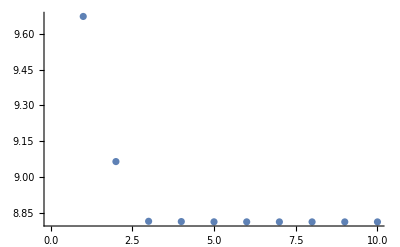

```mathematica
PPLZS[RastringerFunction3D,-2,2,20,0.1,100, 100]
PPLZS[AckleyFunction3D,-5,5,20,0.1,100,100]
```